```mathematica
DSolve[k'[t]==s*k[t]^a-m*k[t],k[t],t]//FullSimplify
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
mk[t_]:=InverseFunction[(0.5* Log[#1]-Log[0.2 #1-0.3 #1^(1/2)])/((-1+0.5) *0.2)&][-t+C[1]]
```

```mathematica
Plot[mk[t],{t,0,10}]
```

$Aborted

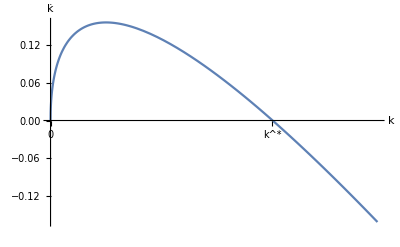

```mathematica
L=Plot[0.5*Sqrt[t]-0.4*t,{t,0,2.3},Ticks->{{{0,"0"},{1.56,"k^*"}},None},AxesLabel->{k,k̇},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"]]
```

```mathematica
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig1.pdf",L,ImageResolution->1500]
```

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig1.pdf

```mathematica
"D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig1.pdf"
```

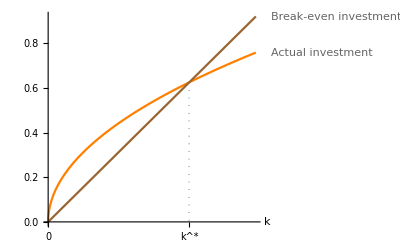

```mathematica
L2=Show[Plot[{0.5*Sqrt[t],0.4*t},{t,0,2.3},Ticks->{{{0,"0"},{1.56,"k^*"}},None},AxesLabel->{k},AxesStyle->Directive[FontSize->13,FontFamily->"Times New Roman"],PlotLabels->{"Actual investment","Break-even investment"},PlotStyle->{Orange,Brown}],ParametricPlot[{1.561,t},{t,0.006,0.615},PlotStyle->{Dotted,Thickness[Medium]}]]
```

```mathematica
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig1.pdf",L2,ImageResolution->1500]
```

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig1.pdf

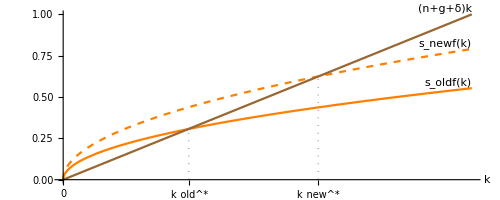

```mathematica
L3=Show[Plot[{0.5*Sqrt[t],0.35*Sqrt[t],0.4*t},{t,0,2.5},Ticks->{{{0,"0"},{0.768,"k_old^*"},{1.56,"k_new^*"}},None},AxesLabel->{k},AxesStyle->Directive[FontSize->13,FontFamily->"Times New Roman"],PlotLabels->Placed[{Style["s_newf(k)",Italic,FontSize->11,FontFamily->"Times New Roman"],Style["s_oldf(k)",Italic,FontSize->11,FontFamily->"Times New Roman"],Style["(n+g+δ)k",Italic,FontSize->11,FontFamily->"Times New Roman"]},{Scaled[1],Above}],PlotStyle->{{Orange,Dashed},Orange,Brown}],ParametricPlot[{1.56,t},{t,0.002,0.622},PlotStyle->{Dotted,Thickness[Medium]}],ParametricPlot[{0.768,t},{t,0.002,0.31},PlotStyle->{Dotted,Thickness[Medium]}]]
```

```mathematica
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig3.pdf",L3,ImageResolution->1500]
```

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig3.pdf

```mathematica
L4=-Graphics-
```

-Graphics-

```mathematica
Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig3.pdf",L4,ImageResolution->1500]
```

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig3.pdf

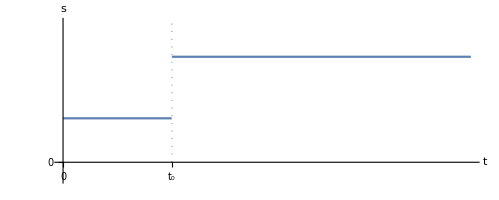

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig4_1.pdf

```mathematica
L5=Show[Plot[Piecewise[{{0.25,t<0.6},{0.6,0.6<t}}],{t,0,2.25},Ticks->{{{0,"0"},{0.6,"t_0"}},{{0,"0"}}},AxesLabel->{t,s},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"],PlotRange->{-0.1,0.8}],ParametricPlot[{0.6,t},{t,0.002,0.8},PlotStyle->{Dotted,Thickness[Medium]}]]

Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig4_1.pdf",L5,ImageResolution->1500]
```

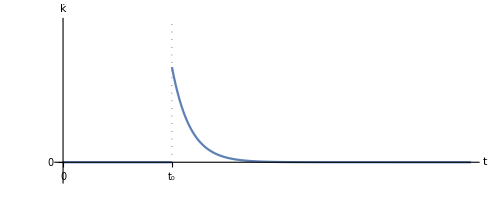

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig4_2.pdf

```mathematica
L6=Show[Plot[Piecewise[{{0,t<6},{2200/E^(t),6<t}}],{t,0,22.5},Ticks->{{{0,"0"},{6,"t_0"}},{{0,"0"}}},AxesLabel->{t,k̇},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"],PlotRange->{-1,8}],ParametricPlot[{6,t},{t,0.002,8},PlotStyle->{Dotted,Thickness[Medium]}]]

Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig4_2.pdf",L6,ImageResolution->1500]
```

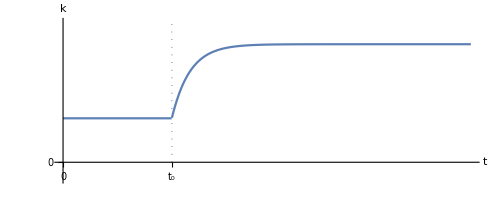

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig4_3.pdf

```mathematica
L7=Show[Plot[Piecewise[{{2.5,t<6},{6.71388-1700/E^(t),6<t}}],{t,0,22.5},Ticks->{{{0,"0"},{6,"t_0"}},{{0,"0"}}},AxesLabel->{t,k},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"],PlotRange->{-1,8}],ParametricPlot[{6,t},{t,0.002,8},PlotStyle->{Dotted,Thickness[Medium]}]]

Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig4_3.pdf",L7,ImageResolution-> 1500]
```

```mathematica
Solve[2.5==x-1700/E^(6),x]
```

{{x→6.71388}}

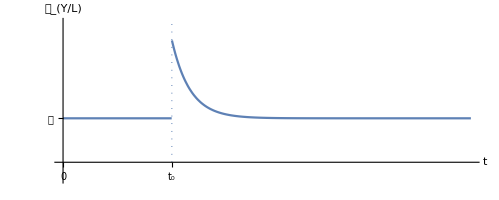

D:\CHY\LaTeX\Notes\Advanced_Macroeconomics\fig4_4.pdf

```mathematica
L8=Show[Plot[Piecewise[{{2.5,t<6},{2.5+1800/E^(t),6<t}}],{t,0,22.5},Ticks->{{{0,"0"},{6,"t_0"}},{{2.5,"ℊ"}}},AxesLabel->{t,Subscript[ℊ, Y/L]},AxesStyle->Directive[FontSize->15,FontFamily->"Times New Roman"],PlotRange->{-1,8}],ParametricPlot[{6,t},{t,0.002,8},PlotStyle->{Dotted,Thickness[Medium]}]]

Export["D:\\CHY\\LaTeX\\Notes\\Advanced_Macroeconomics\\fig4_4.pdf",L8,ImageResolution->1500]
```